```mathematica
GetSlope[p1_,p2_]:=
Module[{x1,x2,y1,y2,m,b},
{x1,y1}=p1;
{x2,y2}=p2;
m=(y2-y1)/(x2-x1);
m
]
```

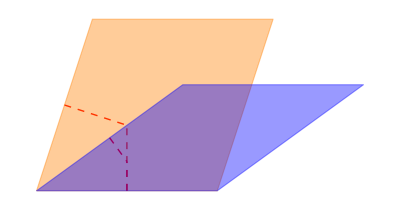

```mathematica
(*construct rhomb*)
a1={1,0};
a2S={Cos[36/180*Pi],Sin[36/180*Pi]};
a2F={Cos[72/180*Pi],Sin[72/180*Pi]};
TileF={EdgeForm[Thick],Orange,Opacity[0.4],Polygon[{{0,0},a2F,a1+a2F,a1}]};
TileS={EdgeForm[Thick],Blue,Opacity[0.4],Polygon[{{0,0},a2S,a1+a2S,a1}]};
mS=GetSlope[{0,0},a1+a2S];
pS={0.5,mS*0.5};
mF=GetSlope[{0,0},a1+a2F];
pF={0.5,mF*0.5};
VorF={{Dashed,Red,Thick,Line[{a1/2,pF}]},{Dashed,Red,Thick,Line[{a2F/2,pF}]}};
VorS={{Dashed,Red,Thick,Line[{a1/2,pS}]},
{Dashed,Red,Thick,Line[{a2S/2,pS}]}};
TileF=Join[VorF,TileF];
TileS=Join[VorS,TileS];
Graphics[{TileF,TileS}]
```

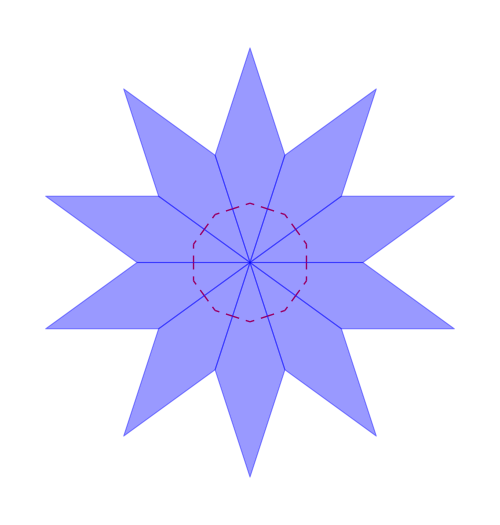

```mathematica
(*Construct ST Tile*)
Graphics[{
Table[Rotate[TileS,x Degree,{0,0}],{x,Range[0,9]*360/10}]
},ImageSize->500]
```

```mathematica
(*Construct Y Tile*)
```

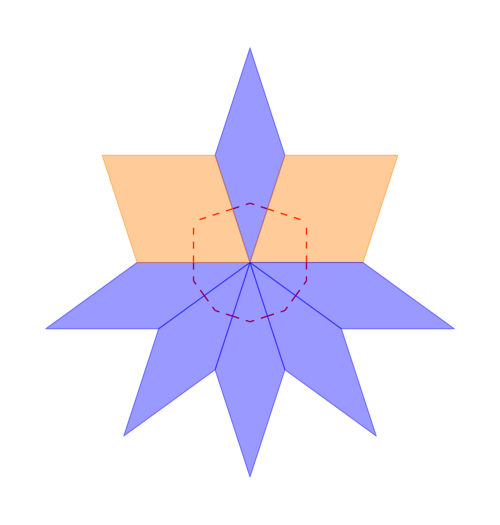

```mathematica
skinny=Table[Rotate[TileS,x Degree,{0,0}],{x,Join[{2},Range[5,9]]*360/10}];
fats=Table[Rotate[TileF,x Degree,{0,0}],{x,{0,36+72}}];
Graphics[{skinny,fats},ImageSize->500]
```

```mathematica
(*Construct Z Tile*)
```

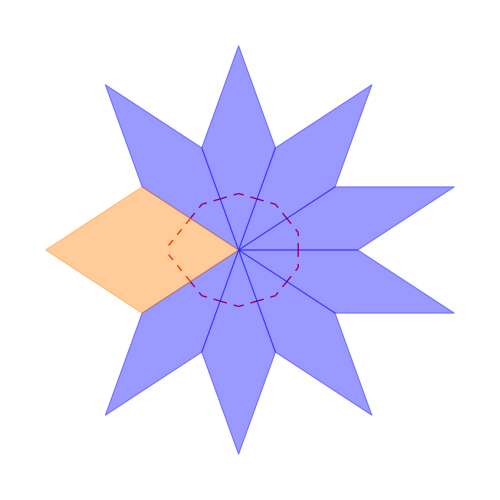

```mathematica
skinny=Table[Rotate[TileS,x Degree,{0,0}],{x,{0,1,2,3,6,7,8,9}*360/10}];
fats=Table[Rotate[TileF,x Degree,{0,0}],{x,{72*2}}];
Graphics[{skinny,fats},AspectRatio->Automatic]
```

```mathematica
(*Construct X Tile*)
```

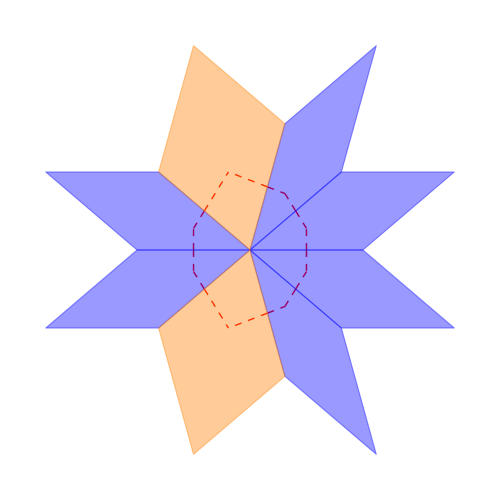

```mathematica
skinny=Table[Rotate[TileS,x Degree,{0,0}],{x,{-2,-1,0,1,4,5}*360/10}];
fats=Table[Rotate[TileF,x Degree,{0,0}],{x,{72,72*3}}];
Graphics[{skinny,fats},AspectRatio->Automatic]
```

```mathematica
GetSlope[p1_,p2_]:=
Module[{x1,x2,y1,y2,m,b},
{x1,y1}=p1;
{x2,y2}=p2;
m=(y2-y1)/(x2-x1);
m
]
```

```mathematica
(*construct rhomb*)
a1={1,0};
a2S={Cos[36/180*Pi],Sin[36/180*Pi]};
a2F={Cos[72/180*Pi],Sin[72/180*Pi]};
TileF={EdgeForm[Thick],Opacity[0.],Polygon[{{0,0},a2F,a1+a2F,a1}]};
TileS={EdgeForm[Thick],Opacity[0.],Polygon[{{0,0},a2S,a1+a2S,a1}]};
mS=GetSlope[{0,0},a1+a2S];
pS={0.5,mS*0.5};
mF=GetSlope[{0,0},a1+a2F];
pF={0.5,mF*0.5};(*
VorF={{Dashed,Red,Thick,Line[{a1/2,pF}]},{Dashed,Red,Thick,Line[{a2F/2,pF}]}};
VorS={{Dashed,Red,Thick,Line[{a1/2,pS}]},
{Dashed,Red,Thick,Line[{a2S/2,pS}]}};
TileF=Join[VorF,TileF];
TileS=Join[VorS,TileS];*)
Graphics[{TileF,TileS}]
```

-Graphics-

```mathematica
(*Construct ST Tile*)
Graphics[{
Table[Rotate[TileS,x Degree,{0,0}],{x,Range[0,9]*360/10}]
},ImageSize->500]
```

-Graphics-

```mathematica
(*Construct Y Tile*)
```

```mathematica
skinny=Table[Rotate[TileS,x Degree,{0,0}],{x,Join[{2},Range[5,9]]*360/10}];
fats=Table[Rotate[TileF,x Degree,{0,0}],{x,{0,36+72}}];
Graphics[{skinny,fats},ImageSize->500]
```

-Graphics-

```mathematica
(*Construct Z Tile*)
```

```mathematica
skinny=Table[Rotate[TileS,x Degree,{0,0}],{x,{0,1,2,3,6,7,8,9}*360/10}];
fats=Table[Rotate[TileF,x Degree,{0,0}],{x,{72*2}}];
Graphics[{skinny,fats},AspectRatio->Automatic]
```

-Graphics-

```mathematica
(*Construct X Tile*)
```

```mathematica
skinny=Table[Rotate[TileS,x Degree,{0,0}],{x,{-2,-1,0,1,4,5}*360/10}];
fats=Table[Rotate[TileF,x Degree,{0,0}],{x,{72,72*3}}];
Graphics[{skinny,fats},AspectRatio->Automatic]
```

-Graphics-